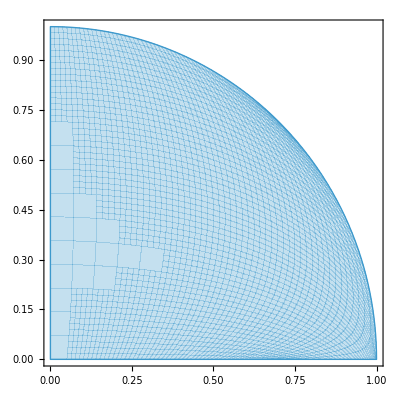

```mathematica
X[x_,y_]:= x*Sqrt[1-y^2/2]
Y[x_,y_]:=y*Sqrt[1-x^2/2]
ParametricPlot[{X[x,y],  (Sqrt[1-X[x,y]^2] +Y[x,y])/2 },{x,0,1},{y,-1,1}]
```